Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11159

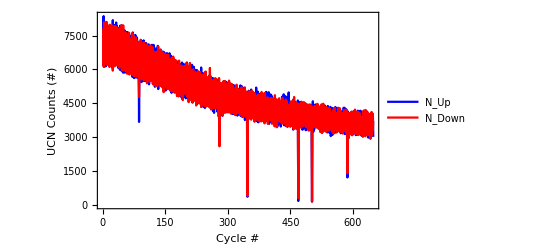

Number of Cycles: 679.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11159];(*11159,11369*)
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[2;;650,27]],metadata[[2;;650,28]],PlotLegends->{"N_Up","N_Down"},PlotStyle->{Blue,Red,Gray},Joined->True,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Cycle #","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

## Making Condition Exp

```mathematica
maxcondi=10;
condi0=StringJoin[Table[StringJoin["(Norm[data[[i-",ToString[k-1],"]][[4]]-data[[i-",ToString[k],"]][[4]]]<100)&&"],{k,1,maxcondi-1}]];
condi=StringJoin[condi0,Table[StringJoin["(Norm[data[[i-",ToString[k-1],"]][[4]]-data[[i-",ToString[k],"]][[4]]]<100)"],{k,maxcondi,maxcondi}]]
```

(Norm[data[[i-0]][[4]]-data[[i-1]][[4]]]<100)&&(Norm[data[[i-1]][[4]]-data[[i-2]][[4]]]<100)&&(Norm[data[[i-2]][[4]]-data[[i-3]][[4]]]<100)&&(Norm[data[[i-3]][[4]]-data[[i-4]][[4]]]<100)&&(Norm[data[[i-4]][[4]]-data[[i-5]][[4]]]<100)&&(Norm[data[[i-5]][[4]]-data[[i-6]][[4]]]<100)&&(Norm[data[[i-6]][[4]]-data[[i-7]][[4]]]<100)&&(Norm[data[[i-7]][[4]]-data[[i-8]][[4]]]<100)&&(Norm[data[[i-8]][[4]]-data[[i-9]][[4]]]<100)&&(Norm[data[[i-9]][[4]]-data[[i-10]][[4]]]<100)

## 11159: 72, 172, 198, 223, 231, 283, 301, 321, 326, 369, 515, 556, 600

```mathematica
Monitor[
Clear[data];
endrun=369;
For[runi=369,runi≤endrun,runi++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure];
(**)
dimdata=Dimensions[data][[1]];
cnt=Table[0,{k,1,dimdata}];j=1;
For[i=maxcondi,i≤dimdata,i++,
If[((Norm[data[[i-0]][[4]]-data[[i-1]][[4]]]<100)&&(Norm[data[[i-1]][[4]]-data[[i-2]][[4]]]<100)&&(Norm[data[[i-2]][[4]]-data[[i-3]][[4]]]<100)&&(Norm[data[[i-3]][[4]]-data[[i-4]][[4]]]<100)&&(Norm[data[[i-4]][[4]]-data[[i-5]][[4]]]<100)&&(Norm[data[[i-5]][[4]]-data[[i-6]][[4]]]<100)&&(Norm[data[[i-6]][[4]]-data[[i-7]][[4]]]<100)&&(Norm[data[[i-7]][[4]]-data[[i-8]][[4]]]<100)&&(Norm[data[[i-8]][[4]]-data[[i-9]][[4]]]<100)&&(Norm[data[[i-9]][[4]]-data[[i-10]][[4]]]<100)
(*&&(data[[i]][[3]]==data[[i-1]][[3]])*)),
cnt[[j]]=i;
j++;
];
];
bdlst=DeleteCases[cnt,0];
bddata=Part[data,bdlst];
gddata=DeleteCases[data,Alternatives@@bddata];
If[Dimensions[bddata][[1]]>0,
Print["Cycle: ",runi];
Print["Total Events: ",Dimensions[data][[1]]];
Print["Bad Events: ",Dimensions[bddata][[1]]," , Good Events: ",Dimensions[gddata][[1]]," , Total Events: ",Dimensions[bddata][[1]]+Dimensions[gddata][[1]]];
];
(**)
gddimdata=Dimensions[gddata][[1]];bddimdata=Dimensions[bddata][[1]];
(**)
];,ProgressIndicator[runi/endrun,ImageSize->{1000,100}]];
(**)
```

Cycle: 369

Total Events: 92351

Bad Events: 175 , Good Events: 92176 , Total Events: 92351

## Ch. by Ch. dist: 11159 (bursts need not be in same ch#)

```mathematica
allbddata=Union[Table[data[[bdlst[[k]]-10]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-9]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-8]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-7]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-6]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-5]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-4]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-3]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-2]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]-1]],{k,1,Dimensions[bdlst][[1]]}],
Table[data[[bdlst[[k]]]],{k,1,Dimensions[bdlst][[1]]}]];
chdist1=Table[{0,0,0},{k,1,3}];chdist2=Table[{0,0,0},{k,1,3}];
For[j=1,j≤Dimensions[allbddata][[1]],j++,
If[allbddata[[j]][[3]]==1,chdist1[[1]][[1]]++];
If[allbddata[[j]][[3]]==2,chdist1[[1]][[2]]++];
If[allbddata[[j]][[3]]==3,chdist1[[1]][[3]]++];
If[allbddata[[j]][[3]]==4,chdist1[[2]][[1]]++];
If[allbddata[[j]][[3]]==5,chdist1[[2]][[2]]++];
If[allbddata[[j]][[3]]==6,chdist1[[2]][[3]]++];
If[allbddata[[j]][[3]]==7,chdist1[[3]][[1]]++];
If[allbddata[[j]][[3]]==8,chdist1[[3]][[2]]++];
If[allbddata[[j]][[3]]==9,chdist1[[3]][[3]]++];
(*Ch2*)
If[allbddata[[j]][[3]]==11,chdist2[[1]][[1]]++];
If[allbddata[[j]][[3]]==12,chdist2[[2]][[1]]++];
If[allbddata[[j]][[3]]==13,chdist2[[3]][[1]]++];
If[allbddata[[j]][[3]]==14,chdist2[[1]][[2]]++];
If[allbddata[[j]][[3]]==15,chdist2[[2]][[2]]++];
If[allbddata[[j]][[3]]==16,chdist2[[3]][[2]]++];
If[allbddata[[j]][[3]]==17,chdist2[[1]][[3]]++];
If[allbddata[[j]][[3]]==18,chdist2[[2]][[3]]++];
If[allbddata[[j]][[3]]==19,chdist2[[3]][[3]]++];
];
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
chdist1[[i]][[j]]=10*chdist1[[i]][[j]]+RandomInteger[{-2,2}];
chdist2[[i]][[j]]=10*chdist2[[i]][[j]]+RandomInteger[{-2,2}];
];
];
lineStyle={Thick,Black};
GraphicsGrid[{{
ArrayPlot[chdist1,ColorFunction->"SouthwestColors",PlotLegends->Automatic,PlotLabel->"NANOSC-A",Ticks->Automatic,Axes->True,ImageSize->500,AxesStyle->Thick,LabelStyle->{28,Black,Bold},AxesLabel->{"     X (m)     ","     Y (m)     "},
Epilog->{
{Directive[lineStyle],
Text[Style["1",FontSize->Large],{.5,2.5}],
Text[Style["2",FontSize->Large],{1.5,2.5}],
Text[Style["3",FontSize->Large],{2.5,2.5}],
Text[Style["4",FontSize->Large],{.5,1.5}],
Text[Style["5",FontSize->Large],{1.5,1.5}],
Text[Style["6",FontSize->Large],{2.5,1.5}],
Text[Style["7",FontSize->Large],{.5,.5}],
Text[Style["8",FontSize->Large],{1.5,.5}],
Text[Style["9",FontSize->Large],{2.5,.5}]
}
}
],
ArrayPlot[chdist2,ColorFunction->"SouthwestColors",PlotLegends->Automatic,PlotLabel->"NANOSC-B",Ticks->Automatic,Axes->True,ImageSize->500,AxesStyle->Thick,LabelStyle->{28,Black,Bold},AxesLabel->{"     X (m)     ","     Y (m)     "},
Epilog->{
{Directive[lineStyle],
Text[Style["11",FontSize->Large],{.5,2.5}],
Text[Style["12",FontSize->Large],{.5,1.5}],
Text[Style["13",FontSize->Large],{.5,.5}],
Text[Style["14",FontSize->Large],{1.5,2.5}],
Text[Style["15",FontSize->Large],{1.5,1.5}],
Text[Style["16",FontSize->Large],{1.5,.5}],
Text[Style["17",FontSize->Large],{2.5,2.5}],
Text[Style["18",FontSize->Large],{2.5,1.5}],
Text[Style["19",FontSize->Large],{2.5,.5}]
}
}
]
}},ImageSize->1200]
```

-Graphics-

## Time of arrival

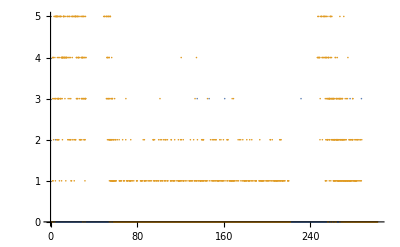

```mathematica
allbddimdata=Dimensions[allbddata][[1]];
histbeg=100000000;histlast=302100000000;binw=100000000;
hst0=HistogramList[allbddata[[2;;allbddimdata,4]],{histbeg,histlast,binw}];
hst2=HistogramList[gddata[[2;;gddimdata,4]],{histbeg,histlast,binw}];
ucnshutter=Table[0,{k,1,310,.1}];
ucnshutter[[280;;300]]=1;
ucnshutter[[2180;;2200]]=-1;
ListPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst0[[2]]}],Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst2[[2]]}]}]
```

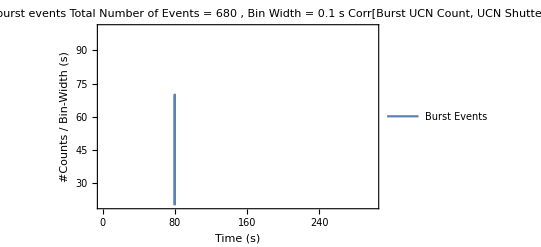
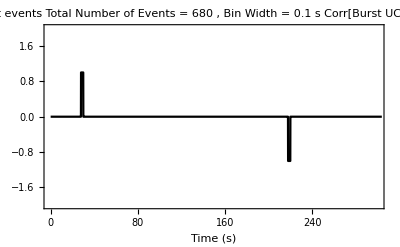

```mathematica
Overlay[{ListPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]/(10^9)+10,5*hst0[[2]]}]},ImagePadding->80,PlotRange->{{0,300},{20,100}},Joined->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->{True,True},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[20*hst0[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter] = 0.99"],Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
ListLinePlot[{Table[{k/10,ucnshutter[[k]]},{k,1,3040}]},ImagePadding->80,PlotStyle->Black,Frame->{True,False,False,True},PlotRange->{{0,300},{-2,2}},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[20*hst0[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter] = 0.99"],FrameLabel->{"Time (s)","","",Rotate["UCN Shutter State {-1=Opening, 1=Closing}",180Degree]}]}]
```

## Number Histogram

```mathematica
maxcondi=3;
condi0=StringJoin[Table[StringJoin["(Norm[data[[i-",ToString[k-1],"]][[4]]-data[[i-",ToString[k],"]][[4]]]<100)&&"],{k,1,maxcondi-1}]];
condi=StringJoin[condi0,Table[StringJoin["(Norm[data[[i-",ToString[k-1],"]][[4]]-data[[i-",ToString[k],"]][[4]]]<100)"],{k,maxcondi,maxcondi}]]
```

(Norm[data[[i-0]][[4]]-data[[i-1]][[4]]]<100)&&(Norm[data[[i-1]][[4]]-data[[i-2]][[4]]]<100)&&(Norm[data[[i-2]][[4]]-data[[i-3]][[4]]]<100)

```mathematica
coubrst={};
numbrst={};
Monitor[
Clear[data];
endrun=600;
For[runi=1,runi≤endrun,runi++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure];
(**)
dimdata=Dimensions[data][[1]];
cnt=Table[0,{k,1,dimdata}];j=1;
For[i=maxcondi,i≤dimdata,i++,
If[((Norm[data[[i-0]][[4]]-data[[i-1]][[4]]]<100)&&(Norm[data[[i-1]][[4]]-data[[i-2]][[4]]]<100)),
cnt[[j]]=i;
j++;
];
];
bdlst=DeleteCases[cnt,0];
bddata=Part[data,bdlst];
gddata=DeleteCases[data,Alternatives@@bddata];
(**)
gddimdata=Dimensions[gddata][[1]];bddimdata=Dimensions[bddata][[1]];
(**)
allbddata=Union[Table[data[[bdlst[[k]]-1]],{k,1,Dimensions[bdlst][[1]]}],Table[data[[bdlst[[k]]]],{k,1,Dimensions[bdlst][[1]]}],Table[data[[bdlst[[k]]-2]],{k,1,Dimensions[bdlst][[1]]}]];
(*Print["# of bursts in Cy #",runi," : ",Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata]][[1]]];*)
numbrst=AppendTo[numbrst,Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata]][[1]]];
For[i=1,i<=Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata]][[1]],i++,
coubrst=AppendTo[coubrst,Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata][[i]]][[1]]];
];
];,ProgressIndicator[runi/endrun,ImageSize->{1000,100}]];
(**)
```

```mathematica
coubrst
numbrst
```

{9,10,15,3,6,25,13,7,6,6,49,15,15,9,32,13,7,9,15,7,49,9,15,27,33,22,6,9,9,9,3,3,3,3,6,12,12,22,7,10,12,24,10,8,9,13,24,9,33,21,12,15,6,13,42,12,14,29,3,3,16,3,3,7,15,22,9,12,13,31,12,15,21,13,13,19,9,10,23,23,3,3,3,15,8,9,6,6,3,6,12,28,15,30,28,21,33,9,3,35,6,6,17,31,5,3,5,6,3,3,13,9,9,22,23,3,3,3,3,3,18,33,3,25,12,3,24,25,12,6,14,18,3,3,40,32,24,46,13,15,6,10,12,9,12,9,6,6,15,19,9,9,12,16,16,9,9,22,9,13,6,9,27,16,13,24,9,3,15,3,3,9,8,6,9,9,10,9,3,3,3,3,7,3,4,3,3,3,22,15,9,18,26,15,9,33,20,18,9,9,3,3,9,16,14,13,12,29,15,23,47,9,13,21,18,27,18,9,3,24,27,3,3,18,3,3,33,7,12,21,27,16,3,3,3,7,28,30,9,6,18,22,5,3,6,3,3,37,3,6,3,9,24,18,10,37,22,29,37,6,14,18,23,15,10,13,5,27,9,3,3,3,3,3,9,9,28,3,3,3,3,16,19,9,26,13,24,17,9,15,24,15,20,24,6,16,17,15,9,3,3,3,28,37,14,13,6,4,3,3,3,3,3,9,12,9,16,10,12,3,3,3,3,7,11,14,15,16,7,6,15,3,27,11,6,24,18,6,9,13,30,31,3,9,3,9,23,10,3,3,31,13,12,18,17,6,3,12,27,18,21,12,11,9,21,9,10,24,33,3,24,12,15,12,28,25,15,6,39,23,12,8,3,3,3,4,12,17,20,20,3,4,3,9,9,15,15,6,29,19,43,24,21,12,9,18,4,3,3,3,3,4,3,21,9,12,9,24,3,3,41,32,15,27,13,31,42,13,19,9,9,4,9,43,13,19,3,3,3,1,3,6,14,23,15,3,4,3,3,4,9,14,9,26,3,18,9,13,10,3,4,3,29,25,38,3,3,3,4,4,4,21,33,27,17,25,16,12,9,3,3,3,3,21,13,12,3,3,3,3,3,21,9,9,9,9,3,3,6,28,22,15,23,14,9,21,15,39,7,3,3,3,3,7,3,9,3,3,3,3,7,6,10,12,21,24,16,19,21,7,25,20,10,7,18,4,3,4,3,14,5,7,26,24,23,6,16,20,3,3,22,9,34,18,3,3,3,6,11,15,3,4,3,3,34,3,12,30,9,15,32,12,11,3,6,16,8,9,12,3,3,12,9,29,35,9,6,9,6,13,25,18,6,15,39,13,13,26,34,29,20,18,4,3,3,3,3,3,4,6,37,29,18,19,25,28,18,4,3,3,3,3,3,15,6,18,9,18,3,3,3,3,36,17,11,15,6,26,24,28,40,26,6,9,3,3,3,3,9,7,6,16,321,17,7,3,3,3,3,3,4,18,6,3,9,9,13,3,3,6,3,3,3,3,27,27,6,7,16,24,15,19,11,20,6,6,3,9,3,3,4,3,42,36,5,7,17,13,14,12,15,30,16,6,7,3,3,3,10,22,16,3,3,12,9,16,9,19,19,18,25,9,12,30,25,7,12,3,3,5,3,3,4,7,15,25,3,3,12,9,12,44,3,5,6,10,13,9,9,9,3,3,9,3,3,12,16,3,3,3,5,3,3,9,8,3,3,3,3,9,8,9,3,3,20,35,43,3,6,6,3,3,17,9,4,3,3,12,9,3,6,6,12,9,23,10,9,36,21,16,38,10,12,18,15,9,17,11,33,25,7,3,3,3,7,26,9,9,17,9,6,11,7,22,6,6,12,31,9,7,36,30,14,44,12,27,12,14,9,20,3,3,3,3,19,9,7,24,3,9,3,3,4,3,3,28,26,15,14,19,26,24,8,6,8,31,9,9,12,24,18,21,6,33,3,3,3,15,6,21,10,22,4,3,26,12,6,17,12,10,3,7,15,22,36,5,3,13,3,9,13,11,24,24,3,3,3,6,20,10,10,3,3,3,3,31,24,16,15,15,3,6,3,10,32,13,6,6,16,20,3,18,25,27,21,14,13,34,3,3,3,9,21,24,24,13,8,3,3,5,3,3,17,6,22,9,6,8,6,9,12,12,9,17,3,3,4,4,18,33,35,34,25,6,6,18,9,6,27,22,27,9,9,13,9,15,6,3,9,27,21,23,37,18,26,6,12,22,22,21,33,6,3,6,3,3,3,28,28,34,28,18,9,6,9,9,10,6,12,15,16,21,16,25,26,35,9,3,5,10,9,6,9,9,9,14,18,17,13,21,6,3,6,6,17,28,23,3,9,21,33,31,22,24,33,12,23,15,9,14,35}

{2,1,2,1,4,1,1,2,1,1,2,2,1,2,1,1,1,3,6,2,1,2,1,1,2,2,2,1,1,1,3,1,2,1,2,1,2,2,2,1,1,1,2,1,2,1,2,1,1,3,2,2,3,2,1,1,1,1,1,2,1,3,1,3,4,2,2,5,1,1,1,3,1,2,2,1,2,1,1,1,1,2,2,2,1,3,1,2,1,2,2,1,2,3,1,2,1,3,2,3,4,4,6,1,1,2,1,2,1,1,1,2,2,2,1,2,1,1,1,1,2,1,1,1,1,2,1,1,2,1,2,1,2,1,2,4,1,1,2,2,5,1,4,1,2,1,1,1,1,2,1,1,2,2,1,2,4,2,1,4,1,2,1,1,1,2,1,1,2,1,2,2,4,1,1,1,2,4,2,2,2,2,4,2,2,1,4,1,2,1,2,2,1,1,4,2,2,1,1,1,1,1,3,1,1,1,2,1,1,2,1,1,1,1,2,1,1,1,2,1,2,5,2,2,3,2,1,2,1,1,1,1,1,2,1,3,4,2,2,1,2,1,1,2,1,1,1,1,2,3,1,2,5,2,1,1,5,2,1,1,1,1,2,4,1,1,1,6,1,1,1,1,1,1,3,3,2,1,5,2,2,4,1,2,1,2,1,1,1,6,2,4,3,1,1,2,1,2,1,1,3,4,3,1,1,1,2,1,2,2,1,1,3,2,1,4,1,2,1,2,1,1,3,1,2,3,2,1,1,3,2,1,1,2,1,2,1,1,1,1,1,3,5,1,1,1,1,1,1,1,4,2,1,2,2,4,1,2,2,1,1,1,1,1,2,4,1,2,2,2,6,1,3,2,5,2,1,1,2,2,1,2,1,4,4,1,1,3,2,2,1,1,2,4,1,1,1,3,2,1,1,1,1,2,1,1,2,6,2,1,2,2,1,1,2,2,2,1,4,2,2,3,3,1,5,3,2,1,1,1,5,2,3,1,3,2,2,2,1,1,1,1,2,1,1,1,2,1,1,5,1,2,1,2,2,1,1,2,1,2,1,1,1,1,1,1,2,2,3,2,2,1,2,5,1,1,2,1,1,2,2,1,1,2,1,1,2,1,3,2,2,1,2,1,2,1,3,2,1,1,2,3,2,1,1,3,2,2,4,1,1,2,2,3,1,2,2,1,2,1,1,1,2,1,4,1,1,1,2,5,2,3,3,1,2,1,4,1,1,1,1,1,2,1,2,1,1,1,2,2,2,2,1,1,1,1,1,2,1,1,2,1,3,3,1,1,1,1,1,3,2,2,2,1,1,1,1,1,1,3,4,2,1,2,1,4,1,1,3,1,1,1,1,1,1,1,1,1,2,1}

Part::partd: Part specification hstpt ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of hstpt ⟦ 2 ⟧ does not exist.

Part::partw: Part 4 of hstpt ⟦ 2 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

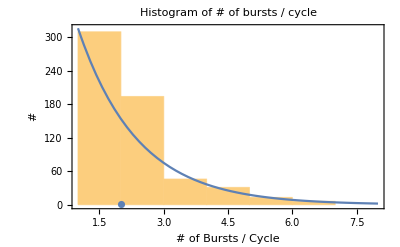

```mathematica
Show[{
Histogram[numbrst,{1,8,1},PlotRange->Full,Frame->True,FrameLabel->{"# of Bursts / Cycle","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of bursts / cycle"],
Plot[650Exp[-.72xx],{xx,1,8},PlotRange->Full,Frame->True,FrameLabel->{"# of Bursts / Cycle","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of bursts / cycle"],
EDAListPlot[Table[{k,{hstpt[[2]][[k]],2Sqrt[hstpt[[2]][[k]]]}},{k,1,8}],PlotRange->Full,Frame->True,FrameLabel->{"# of Bursts / Cycle","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of bursts / cycle"]
}]
```

Part::partd: Part specification hstpt2 ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of hstpt2 ⟦ 2 ⟧ does not exist.

Part::partw: Part 4 of hstpt2 ⟦ 2 ⟧ does not exist.

Part::partw: Part 5 of hstpt2 ⟦ 2 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

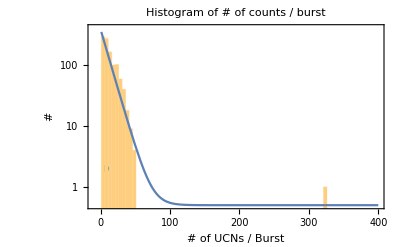

```mathematica
Show[{
EDALogListPlot[Table[{k,hstpt2[[2]][[((k-1)/5)+1]]+.05},{k,1,395,5}],PlotRange->{{-10,400},{0.5,400}},Frame->True,FrameLabel->{"# of UCNs / Burst","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of counts / burst"],
Histogram[coubrst,{1,400,5},ScalingFunctions->{Automatic,"Log"},Frame->True,FrameLabel->{"# of UCNs / Burst","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of bursts / cycle"],
LogPlot[380Exp[-.09xx]+.5,{xx,1,400},PlotRange->{{-10,400},{0.5,400}},Frame->True,FrameLabel->{"# of UCNs / Burst","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},ImageSize->{1000},PlotLabel->"Histogram of # of counts / burst"]
}]
```

```mathematica
hstpt=HistogramList[numbrst,{1,10,1}];
hstpt2=HistogramList[coubrst,{1,400,5}]
FindFit[Table[{k,hstpt[[2]][[k]]},{k,1,8}],a1 Exp[-a2 xx],{a1,a2,a3},xx]
FindFit[Table[{k,hstpt2[[2]][[((k-1)/5)+1]]},{k,1,395,5}],a1 Exp[-a2 xx],{a1,a2,a3},xx]
```

{{1,6,11,16,21,26,31,36,41,46,51,56,61,66,71,76,81,86,91,96,101,106,111,116,121,126,131,136,141,146,151,156,161,166,171,176,181,186,191,196,201,206,211,216,221,226,231,236,241,246,251,256,261,266,271,276,281,286,291,296,301,306,311,316,321,326,331,336,341,346,351,356,361,366,371,376,381,386,391,396},{292,272,164,100,102,59,40,18,9,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{a1→656.446,a2→0.718063,a3→1.}

{a1→340.51,a2→0.0668537,a3→1.}

```mathematica
Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata]][[1]]
Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata][[1]]][[1]]
Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata][[2]]][[1]]
```

1

35

Part::partw: Part 2 of {{{7012., "QDC_X3", 14., 4.55042×10^9, 284.746, 5641.39, 253.529}, {7014., "QDC_X3", 11., 4.55042×10^9, 397.944, 6810.57, 369.937}, {7015., "QDC_X3", 15., 4.55042×10^9, 33.843, 391.526, 31.509}, {240501., "QDC_X3", 13., 6.98898×10^10, 187.886, 1515.41, 189.928}, {240503., "QDC_X3", 14., 6.98898×10^10, 330.259, 2696.7, 333.906}, {240504., "QDC_X3", 11., 6.98898×10^10, 393.276, 2525.37, 408.447}, {240505., "QDC_X3", 19., 6.98898×10^10, 203.057, 1031.33, 197.805}, {240506., "QDC_X3", 12., 6.98898×10^10, 597.5, 3589.6, 621.277}, « 19 », {636183., "QDC_X3", 7., 2.31455×10^11, 18.38, 262.865, 10.065}, {636184., "QDC_X3", 8., 2.31455×10^11, -2.334, 219.395, -3.501}, {750253., "QDC_X3", 4., 2.76744×10^11, 12.108, 481.311, 2.48}, {750254., "QDC_X3", 7., 2.76744×10^11, 193.721, 356.151, 216.915}, {750255., "QDC_X3", 8., 2.76744×10^11, 64.185, 1067., 53.828}, {775452., "QDC_X3", 11., 2.87204×10^11, 77.021, 390.942, 99.194}, {775453., "QDC_X3", 15., 2.87204×10^11, 87.524, 1204.92, 89.858}, {775454., "QDC_X3", 18., 2.87204×10^11, 35.01, 414.72, 40.553}}} does not exist.

2

```mathematica
FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata][[1]]
```

{{7012.,QDC_X3,14.,4.55042×10^9,284.746,5641.39,253.529},{7014.,QDC_X3,11.,4.55042×10^9,397.944,6810.57,369.937},{7015.,QDC_X3,15.,4.55042×10^9,33.843,391.526,31.509},{240501.,QDC_X3,13.,6.98898×10^10,187.886,1515.41,189.928},{240503.,QDC_X3,14.,6.98898×10^10,330.259,2696.7,333.906},{240504.,QDC_X3,11.,6.98898×10^10,393.276,2525.37,408.447},{240505.,QDC_X3,19.,6.98898×10^10,203.057,1031.33,197.805},{240506.,QDC_X3,12.,6.98898×10^10,597.5,3589.6,621.277},{240507.,QDC_X3,15.,6.98898×10^10,250.32,1294.19,278.328},{240508.,QDC_X3,16.,6.98898×10^10,131.797,848.768,142.081},{240509.,QDC_X3,17.,6.98898×10^10,151.709,898.146,146.166},{240510.,QDC_X3,18.,6.98898×10^10,147.041,363.372,174.757},{240512.,QDC_X3,9.,6.98898×10^10,50.181,262.865,52.879},{240514.,QDC_X3,6.,6.98898×10^10,59.444,334.489,76.073},{240515.,QDC_X3,4.,6.98898×10^10,54.849,827.47,66.081},{240516.,QDC_X3,7.,6.98898×10^10,50.764,467.599,62.142},{240517.,QDC_X3,8.,6.98898×10^10,94.526,1081.,93.505},{398381.,QDC_X3,11.,1.35527×10^11,-22.173,377.741,-29.904},{398383.,QDC_X3,6.,1.35527×10^11,45.804,204.953,53.098},{398385.,QDC_X3,7.,1.35527×10^11,31.509,383.43,47.847},{424867.,QDC_X3,14.,1.4654×10^11,10.503,216.039,14.296},{424869.,QDC_X3,11.,1.4654×10^11,7.002,325.591,-1.167},{424870.,QDC_X3,17.,1.4654×10^11,49.014,254.769,40.991},{459469.,QDC_X3,14.,1.60933×10^11,70.02,243.245,79.793},{459471.,QDC_X3,11.,1.60933×10^11,54.849,779.915,54.995},{459472.,QDC_X3,15.,1.60933×10^11,17.505,311.368,10.649},{636182.,QDC_X3,9.,2.31455×10^11,3.501,188.98,-13.056},{636183.,QDC_X3,7.,2.31455×10^11,18.38,262.865,10.065},{636184.,QDC_X3,8.,2.31455×10^11,-2.334,219.395,-3.501},{750253.,QDC_X3,4.,2.76744×10^11,12.108,481.311,2.48},{750254.,QDC_X3,7.,2.76744×10^11,193.721,356.151,216.915},{750255.,QDC_X3,8.,2.76744×10^11,64.185,1067.,53.828},{775452.,QDC_X3,11.,2.87204×10^11,77.021,390.942,99.194},{775453.,QDC_X3,15.,2.87204×10^11,87.524,1204.92,89.858},{775454.,QDC_X3,18.,2.87204×10^11,35.01,414.72,40.553}}

## Test

```mathematica
TableForm[allbddata]
```

7012. | QDC_X3 | 14. | 4.55042×10^9 | 284.746 | 5641.39 | 253.529
7014. | QDC_X3 | 11. | 4.55042×10^9 | 397.944 | 6810.57 | 369.937
7015. | QDC_X3 | 15. | 4.55042×10^9 | 33.843 | 391.526 | 31.509
240501. | QDC_X3 | 13. | 6.98898×10^10 | 187.886 | 1515.41 | 189.928
240503. | QDC_X3 | 14. | 6.98898×10^10 | 330.259 | 2696.7 | 333.906
240504. | QDC_X3 | 11. | 6.98898×10^10 | 393.276 | 2525.37 | 408.447
240505. | QDC_X3 | 19. | 6.98898×10^10 | 203.057 | 1031.33 | 197.805
240506. | QDC_X3 | 12. | 6.98898×10^10 | 597.5 | 3589.6 | 621.277
240507. | QDC_X3 | 15. | 6.98898×10^10 | 250.32 | 1294.19 | 278.328
240508. | QDC_X3 | 16. | 6.98898×10^10 | 131.797 | 848.768 | 142.081
240509. | QDC_X3 | 17. | 6.98898×10^10 | 151.709 | 898.146 | 146.166
240510. | QDC_X3 | 18. | 6.98898×10^10 | 147.041 | 363.372 | 174.757
240512. | QDC_X3 | 9. | 6.98898×10^10 | 50.181 | 262.865 | 52.879
240514. | QDC_X3 | 6. | 6.98898×10^10 | 59.444 | 334.489 | 76.073
240515. | QDC_X3 | 4. | 6.98898×10^10 | 54.849 | 827.47 | 66.081
240516. | QDC_X3 | 7. | 6.98898×10^10 | 50.764 | 467.599 | 62.142
240517. | QDC_X3 | 8. | 6.98898×10^10 | 94.526 | 1081. | 93.505
398381. | QDC_X3 | 11. | 1.35527×10^11 | -22.173 | 377.741 | -29.904
398383. | QDC_X3 | 6. | 1.35527×10^11 | 45.804 | 204.953 | 53.098
398385. | QDC_X3 | 7. | 1.35527×10^11 | 31.509 | 383.43 | 47.847
424867. | QDC_X3 | 14. | 1.4654×10^11 | 10.503 | 216.039 | 14.296
424869. | QDC_X3 | 11. | 1.4654×10^11 | 7.002 | 325.591 | -1.167
424870. | QDC_X3 | 17. | 1.4654×10^11 | 49.014 | 254.769 | 40.991
459469. | QDC_X3 | 14. | 1.60933×10^11 | 70.02 | 243.245 | 79.793
459471. | QDC_X3 | 11. | 1.60933×10^11 | 54.849 | 779.915 | 54.995
459472. | QDC_X3 | 15. | 1.60933×10^11 | 17.505 | 311.368 | 10.649
636182. | QDC_X3 | 9. | 2.31455×10^11 | 3.501 | 188.98 | -13.056
636183. | QDC_X3 | 7. | 2.31455×10^11 | 18.38 | 262.865 | 10.065
636184. | QDC_X3 | 8. | 2.31455×10^11 | -2.334 | 219.395 | -3.501
750253. | QDC_X3 | 4. | 2.76744×10^11 | 12.108 | 481.311 | 2.48
750254. | QDC_X3 | 7. | 2.76744×10^11 | 193.721 | 356.151 | 216.915
750255. | QDC_X3 | 8. | 2.76744×10^11 | 64.185 | 1067. | 53.828
775452. | QDC_X3 | 11. | 2.87204×10^11 | 77.021 | 390.942 | 99.194
775453. | QDC_X3 | 15. | 2.87204×10^11 | 87.524 | 1204.92 | 89.858
775454. | QDC_X3 | 18. | 2.87204×10^11 | 35.01 | 414.72 | 40.553

```mathematica
FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata];
Dimensions[FindClusters[Drop[Drop[allbddata,None,3],None,-3]->allbddata]][[2]]
```

35

```mathematica
a={{1,2,3},{2,3,4},{3,4,5}};
b={8,9,0};
MatrixForm[a]
MatrixForm[b]
MatrixForm[Transpose[{a,b}]]
MatrixForm[Join[a,b]]
MatrixForm[ParallelTable[Append[a[[k]],b[[k]]],{k,1,3}]]
```

(1 | 2 | 3
2 | 3 | 4
3 | 4 | 5)

(8
9
0)

({1,2,3} | 8
{2,3,4} | 9
{3,4,5} | 0)

({1,2,3}
{2,3,4}
{3,4,5}
8
9
0)

Part::partd: Part specification EDA`ErrorPropagation`a ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification EDA`ErrorPropagation`a ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification EDA`ErrorPropagation`a ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification EDA`ErrorPropagation`b ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification EDA`ErrorPropagation`b ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification EDA`ErrorPropagation`b ⟦ 3 ⟧ is longer than depth of object.

Part::pkspec1: The expression EDA`ErrorPropagation`b ⟦ 1 ⟧ cannot be used as a part specification.

Part::pkspec1: The expression EDA`ErrorPropagation`b ⟦ 2 ⟧ cannot be used as a part specification.

Part::pkspec1: The expression EDA`ErrorPropagation`b ⟦ 3 ⟧ cannot be used as a part specification.

Part::partw: Part 8 of {1, 2, 3} does not exist.

Part::partw: Part 9 of {2, 3, 4} does not exist.

({{1,2,3},{2,3,4},{3,4,5}}⟦1,8⟧
{{1,2,3},{2,3,4},{3,4,5}}⟦2,9⟧
List)

```mathematica
Append[a[[1]],b[[1]]]
b[[1]]
```

{1,2,3,8}

8

-Graphics3D-

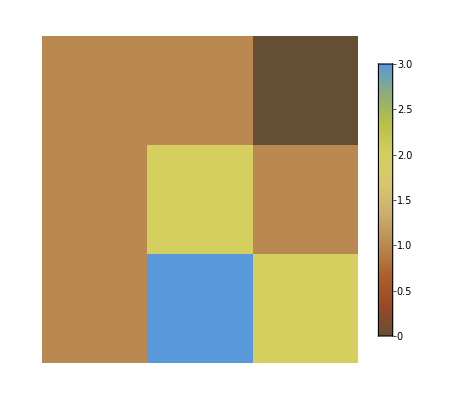

```mathematica
pttab=Flatten[Table[{x,y,z,x+y+z},{x,1,3,1},{y,1,3,1},{z,1,3,1}],2];
pttab2=Table[{x,y,Abs[x-y]},{x,1,3,1},{y,1,3,1}];
ListPlot3D[Flatten[pttab2,1],Mesh->None,InterpolationOrder->0,ColorFunction->"SouthwestColors",Filling->Axis,PlotLegends->Automatic,PlotRange->{{0.5,3.5},{0.5,3.5},{0,10}}]
ArrayPlot[pttab2[[1]],ColorFunction->"SouthwestColors",PlotLegends->Automatic]
```

```mathematica
Normal[ListPlot3D[Flatten[pttab2,1],InterpolationOrder->0,ColorFunction->Hue,Mesh->None,PlotLegends->Automatic,PlotRange->Full]]/.{Line[__]:>Sequence[],Polygon[x:{__},VertexColors->{col_,___},___]:>{col,EdgeForm[],Opacity[.9],Cuboid@@({{1,1,0},1} Sort[x][[{1,-1}]])}}
```

-Graphics3D-

```mathematica
aa={2,3,4};
AppendTo[aa,1]
```

{2,3,4,1}